```mathematica
repBase5BareNull=Table[allGraphs5[k,"colofourrealnull"]->allGraphs5[k,"graph"],{k,allGraphs5NullAtomKeys}];
```

```mathematica
Take[repBase5BareNull,3]
```

{n1x2x3x4x5→-Graphics-,n12x3x4x5→-Graphics-,n123x4x5→-Graphics-}

```mathematica
SummaryPrintGood5Bis[k_]:=Block[
{g=MobiusGraphDoubleGood5[K5Key,k,allGraphs5], gr=allGraphs5[k,"graph"]},
Framed[
Labeled[
Column[{
TableForm[{Labeled[Graph[gr,ImageSize->70],Style[k,Bold,12, Underlined,Red]]}, TableDirections->Row],
Graph[g,ImageSize->1200]
},Alignment->Center],
{Style[StandardForm[allGraphs5[k,"colofourrealnull"]],Darker[Green],12],
Column[
{Style[TraditionalForm[ ChromaticPolynomial[gr,x]],Blue],Style[TraditionalForm[ ChromaticPolynomial[gr,x]//Factor],Red],
Framed[Style[StandardForm[((allGraphs5[k,"colofour"]/.rep5))],Darker[Green],12],Background->Lighter[LightGray, 0.7]]},
Center
]
},
{Top,Bottom,Bottom}
]
]
]
```

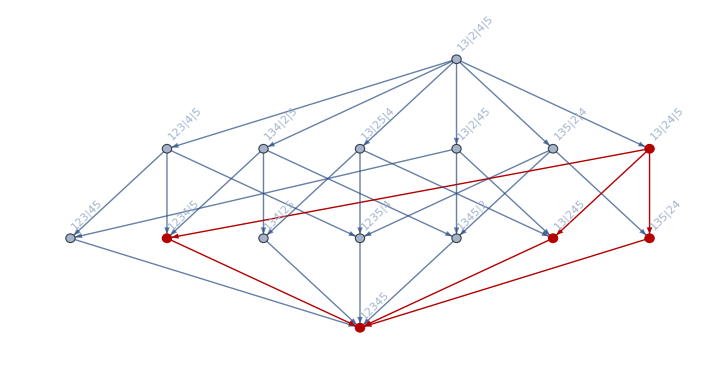

```mathematica
MobiusGraphDoubleGood5[quad1Key,alfa1Key,allGraphs5]
```

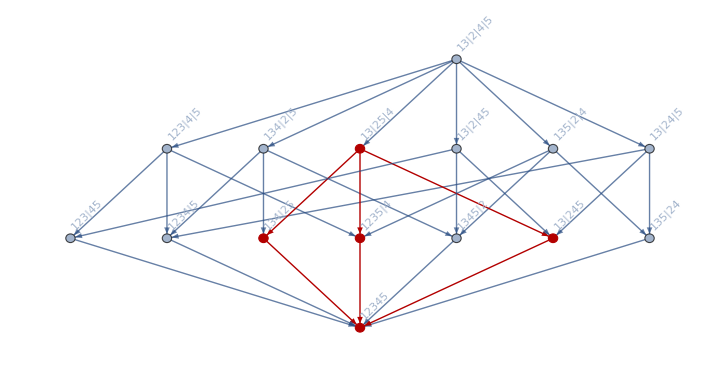

```mathematica
MobiusGraphDoubleGood5[quad1Key,delta1Key,allGraphs5]
```

```mathematica
allGraphs5[quad1Key,"colofourrealnull"]
```

-6 n12345+2 n1234x5+2 n1235x4+n123x45-n123x4x5+2 n1345x2+n134x25-n134x2x5+n135x24-n135x2x4+2 n13x245-n13x24x5-n13x25x4-n13x2x45+n13x2x4x5

```mathematica
allGraphs5[delta1Key,"colofourrealnull"]
```

2 n12345-n1235x4-n134x25-n13x245+n13x25x4

```mathematica
allGraphs5[quad1Key,"colofourrealnull"]+3*allGraphs5[delta1Key,"colofourrealnull"]//Simplify
```

2 n1234x5-n1235x4+n123x45-n123x4x5+2 n1345x2-2 n134x25-n134x2x5+n135x24-n135x2x4-n13x245-n13x24x5+2 n13x25x4-n13x2x45+n13x2x4x5

25

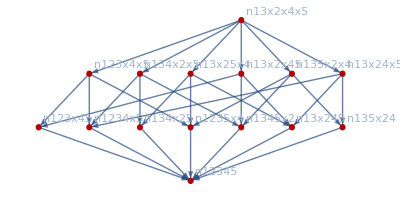

```mathematica
With[{n=ListofVars[2*allGraphs5[quad1Key,"colofourrealnull"]+3*allGraphs5[delta1Key,"colofourrealnull"]+3*allGraphs5[alfa1Key,"colofourrealnull"]],g=MobiusGraphDoubleGood5[quad1Key,quad1Key,allGraphs5]},
Print[Length[n]];
Graph[VertexList[g],EdgeList[g],VertexLabels->"Name",GraphHighlight->n]
]
```

```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,1<->5]&&EdgeQ[g,1<->3]&&EdgeQ[g,1<->4]&&EdgeCount[g]==7]&]
```

{29413}

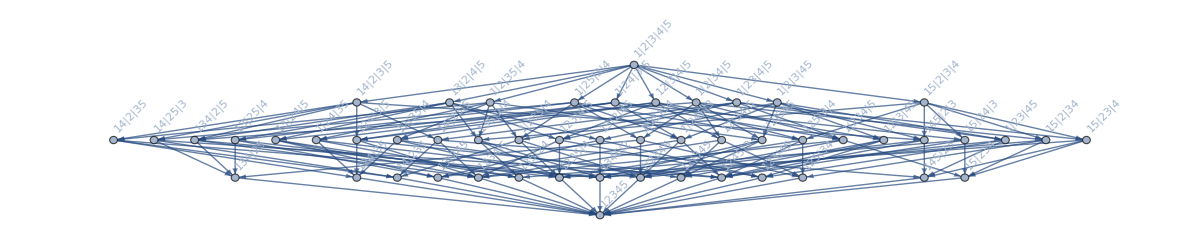
-Graphics-29413
-Graphics-8 n12345-4 n1234x5-2 n1235x4-2 n123x45+2 n123x4x5-2 n1245x3+n124x3x5-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-4 n1345x2+2 n134x2x5+n135x2x4+n13x2x45-n13x2x4x5-2 n145x23+2 n145x2x3+n14x23x5-n14x2x3x5-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5x^5-7 x^4+18 x^3-20 x^2+8 x
(x-2)^3 (x-1) x
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
SummaryPrintGood5Bis[29413]
```

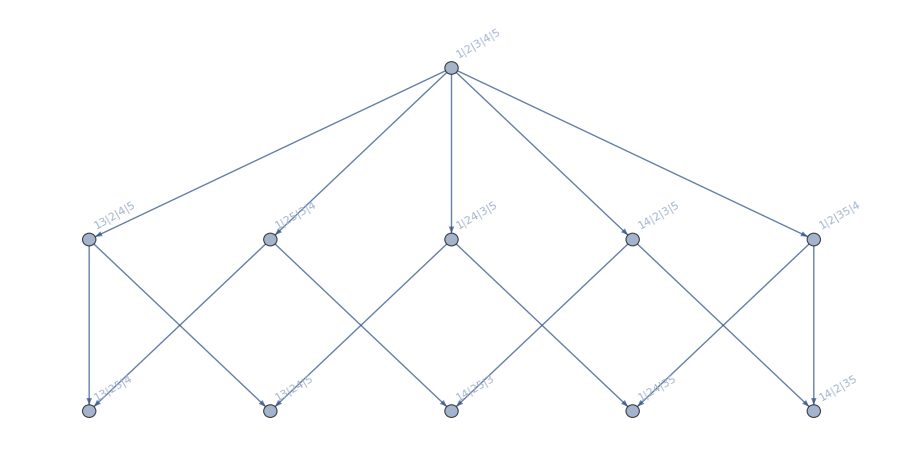

```mathematica
FormulaGraph[allGraphs5[lambdaKey,"colofour"]]
```

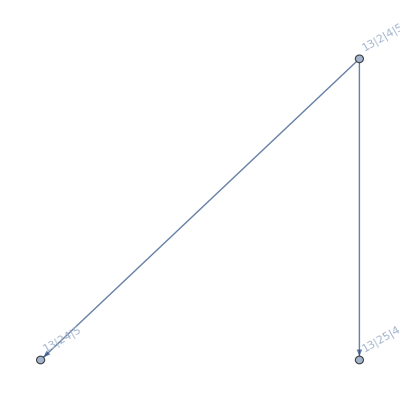

```mathematica
FormulaGraph[allGraphs5[alfaKey,"colofour"]]
```

```mathematica
Monitor[Table[SummaryPrintGood5Bis[k],{k,{lambdaKey,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key,alfaKey,betaKey,gammaKey,deltaKey,epsilonKey, alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}],k]
```

{-Graphics-20665
-Graphics-4 n12345-n1234x5-n1235x4-n123x45+n123x4x5-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5x^5-5 x^4+10 x^3-10 x^2+4 x
(x-2) (x-1) x (x^2-2 x+2)
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-36085
-Graphics--6 n12345+2 n1234x5+2 n1235x4+n123x45-n123x4x5+2 n1345x2+n134x25-n134x2x5+n135x24-n135x2x4+2 n13x245-n13x24x5-n13x25x4-n13x2x45+n13x2x4x5x^4-6 x^3+11 x^2-6 x
(x-3) (x-2) (x-1) x
-Graphics-,-Graphics-29605
-Graphics--6 n12345+2 n1234x5+2 n1245x3+n124x35-n124x3x5+2 n135x24+n13x245-n13x24x5+n15x234-n15x24x3+2 n1x2345-n1x234x5-n1x245x3-n1x24x35+n1x24x3x5x^4-6 x^3+11 x^2-6 x
(x-3) (x-2) (x-1) x
-Graphics-,-Graphics-29527
-Graphics--6 n12345+2 n1235x4+2 n124x35+n12x345-n12x35x4+2 n1345x2+n135x24-n135x2x4+n14x235-n14x2x35+2 n1x2345-n1x235x4-n1x24x35-n1x2x345+n1x2x35x4x^4-6 x^3+11 x^2-6 x
(x-3) (x-2) (x-1) x
-Graphics-,-Graphics-31711
-Graphics--6 n12345+2 n1234x5+2 n1245x3+n124x35-n124x3x5+2 n1345x2+n134x25-n134x2x5+n145x23-n145x2x3+2 n14x235-n14x23x5-n14x25x3-n14x2x35+n14x2x3x5x^4-6 x^3+11 x^2-6 x
(x-3) (x-2) (x-1) x
-Graphics-,-Graphics-29551
-Graphics--6 n12345+2 n1235x4+2 n1245x3+n125x34-n125x3x4+2 n134x25+n13x245-n13x25x4+n14x235-n14x25x3+2 n1x2345-n1x235x4-n1x245x3-n1x25x34+n1x25x3x4x^4-6 x^3+11 x^2-6 x
(x-3) (x-2) (x-1) x
-Graphics-,-Graphics-35977
-Graphics--2 n12345+n1234x5+n1235x4+n123x45-n123x4x5+2 n1345x2-n134x2x5-n135x2x4-n13x2x45+n13x2x4x5x^4-4 x^3+5 x^2-2 x
(x-2) (x-1)^2 x
-Graphics-+-Graphics-+-Graphics-,-Graphics-31681
-Graphics--2 n12345+2 n1234x5+n1245x3-n124x3x5+n1345x2-n134x2x5+n145x23-n145x2x3-n14x23x5+n14x2x3x5x^4-4 x^3+5 x^2-2 x
(x-2) (x-1)^2 x
-Graphics-+-Graphics-+-Graphics-,-Graphics-23041
-Graphics--2 n12345+n1234x5+2 n1245x3-n124x3x5+n15x234-n15x24x3+n1x2345-n1x234x5-n1x245x3+n1x24x3x5x^4-4 x^3+5 x^2-2 x
(x-2) (x-1)^2 x
-Graphics-+-Graphics-+-Graphics-,-Graphics-20803
-Graphics--2 n12345+n1235x4+n1245x3+n125x34-n125x3x4+2 n1x2345-n1x235x4-n1x245x3-n1x25x34+n1x25x3x4x^4-4 x^3+5 x^2-2 x
(x-2) (x-1)^2 x
-Graphics-+-Graphics-+-Graphics-,-Graphics-27259
-Graphics--2 n12345+2 n1235x4+n12x345-n12x35x4+n1345x2-n135x2x4+n1x2345-n1x235x4-n1x2x345+n1x2x35x4x^4-4 x^3+5 x^2-2 x
(x-2) (x-1)^2 x
-Graphics-+-Graphics-+-Graphics-,-Graphics-36166
-Graphics-2 n12345-n1234x5-n135x24-n13x245+n13x24x5x^3-3 x^2+2 x
(x-2) (x-1) x
-Graphics-,-Graphics-31738
-Graphics-2 n12345-n1245x3-n134x25-n14x235+n14x25x3x^3-3 x^2+2 x
(x-2) (x-1) x
-Graphics-,-Graphics-29608
-Graphics-2 n12345-n124x35-n135x24-n1x2345+n1x24x35x^3-3 x^2+2 x
(x-2) (x-1) x
-Graphics-,-Graphics-36112
-Graphics-2 n12345-n1235x4-n134x25-n13x245+n13x25x4x^3-3 x^2+2 x
(x-2) (x-1) x
-Graphics-,-Graphics-31714
-Graphics-2 n12345-n124x35-n1345x2-n14x235+n14x2x35x^3-3 x^2+2 x
(x-2) (x-1) x
-Graphics-}

```mathematica
Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},IsomorphicGraphQ[g,WheelGraph[6]]&&VertexDegree[g,6]==5]&]
```

{6443752,6439540,5393992,5376730,5039860,5026810,2207452,2194402,1857532,1840270,794722,790510}

```mathematica
Table[Labeled[allGraphs6[k,"graph"],Style[k,Red,Underlined]],{k,Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},IsomorphicGraphQ[g,WheelGraph[6]]&&VertexDegree[g,6]==5&&EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,1<->6]]&]}]
```

{-Graphics-5039860}

```mathematica
repBase6Bare=Table[allGraphs6[k,"colofour"]->allGraphs6[k,"graph"],{k,allGraphs6AtomKeys}];
```

```mathematica
allGraphs6[5039860,"colofour"]/.repBase6Bare
```

-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
Table[Labeled[allGraphs6[k,"graph"],Style[k,Red,Underlined]],{k,Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexDegree[g,6]==0&&EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,1<->5]&&EdgeCount[g]==5]&]}]
```

{-Graphics-4980051}

```mathematica
allGraphs6[4980051,"colofour"]/.repBase6Bare
```

-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
Table[Labeled[allGraphs6[k,"graph"],Style[k,Red,Underlined]],{k,Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexDegree[g,6]==1&&EdgeQ[g,1<->6]
&& EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,1<->5]&&EdgeCount[g]==6]&]}]
```

{-Graphics-5039100}

```mathematica
allGraphs6[5039100,"colofour"]/.repBase6Bare
```

-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
Table[Labeled[allGraphs6[k,"graph"],Style[k,Red,Underlined]],{k,Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexDegree[g,6]==2&&EdgeQ[g,1<->6]&&EdgeQ[g,2<->6]
&& EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,1<->5]&&EdgeCount[g]==7]&]}]
```

{-Graphics-5039829}

```mathematica
allGraphs6[5039829,"colofour"]/.repBase6Bare
```

-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
Table[Labeled[allGraphs6[k,"graph"],Style[k,Red,Underlined]],{k,Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexDegree[g,6]==3&&EdgeQ[g,1<->6]&&EdgeQ[g,2<->6]&&EdgeQ[g,3<->6]
&& EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,1<->5]&&EdgeCount[g]==8]&]}]
```

{-Graphics-5039856}

```mathematica
allGraphs6[5039829,"colofour"]/.repBase6Bare
```

```mathematica
Table[
Table[Labeled[allGraphs6[k,"graph"],Style[k,Red,Underlined]]->(allGraphs6[k,"colofour"]/.repBase6Bare),{k,Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexDegree[g,6]==m&&Fold[And,Table[EdgeQ[g,w<->6],{w,m}]]
&& EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,1<->5]&&EdgeCount[g]==5+m]&]}]
,{m,1,5}]//TableForm
```

-Graphics-5039100→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-5039829→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-5039856→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-5039859→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-5039860→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
Table[Labeled[allGraphs5[k,"graph"],Style[k,Red,Underlined]]->(allGraphs5[k,"colofour"]/.repBase5Bare),{k,{lambdaKey,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key,alfaKey,betaKey,gammaKey,deltaKey,epsilonKey, alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]//TableForm
```

-Graphics-20665→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-36085→-Graphics-
-Graphics-29605→-Graphics-
-Graphics-29527→-Graphics-
-Graphics-31711→-Graphics-
-Graphics-29551→-Graphics-
-Graphics-35977→-Graphics-+-Graphics-+-Graphics-
-Graphics-31681→-Graphics-+-Graphics-+-Graphics-
-Graphics-23041→-Graphics-+-Graphics-+-Graphics-
-Graphics-20803→-Graphics-+-Graphics-+-Graphics-
-Graphics-27259→-Graphics-+-Graphics-+-Graphics-
-Graphics-36166→-Graphics-
-Graphics-31738→-Graphics-
-Graphics-29608→-Graphics-
-Graphics-36112→-Graphics-
-Graphics-31714→-Graphics-

```mathematica
Table[Labeled[allGraphs5[k,"graph"],Style[k,Red,Underlined]],{k,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexDegree[g,5]==0&&EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->1]&&EdgeCount[g]==4]&]}]
```

{-Graphics-22122}

```mathematica
allGraphs5[22122,"colofour"]/.repBase5Bare
```

-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
Table[Labeled[allGraphs5[k,"graph"],Style[k,Red,Underlined]],{k,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexDegree[g,5]==4&&EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->1]&&EdgeCount[g]==8]&]}]
```

{-Graphics-22882}

```mathematica
allGraphs5[22882,"colofour"]/.repBase5Bare
```

-Graphics-+-Graphics-+-Graphics-+-Graphics-